20

0.5

{2.90887×10^-8,{w0→1.03755,w1→-0.70642,w2→-1.05963,w3→-2.38416,w4→0.1272,w5→-1.70499,w6→-0.55333,w7→-2.01908,w8→-0.441541}}

{1.03755,0.33113,-0.02208,-1.34661,1.16475,-0.66744,0.48422,-0.98153}

{1.03755,0.33113,-0.02208,-1.34661,1.16475,-0.66744,0.48422,-0.98153}

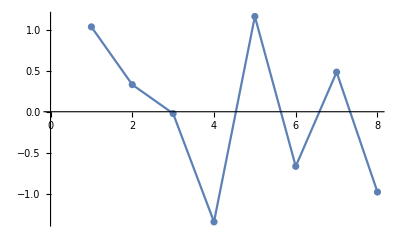

6.07354×10^-17

{1.03755,-0.70642,-1.05963,-2.38416,0.1272,-1.70499,-0.55333,-2.01908,-0.441541}

```mathematica
y={1.03755,0.33113,-0.02208,-1.34661,1.16475,-0.66744,0.48422,-0.98153};

w={w0,w1,w2,w3,w4,w5,w6,w7,w8};

t={1,2,3,4,5,6,7,8};

h=20
h1=0.5

a=RandomChoice[{0},{8,8}];

For[k1=2,k1<9,k1++,
For[k2=2,k2<9,k2++,

a[[k1,k2]]=  Exp[-h*((t[[k1]]-t[[k2]])^2)] ;   
]
  ]


T=NMinimize[        {

(
∑_(i=1)^8 h1*(
(w0+(∑_(j=2)^8 w[[j]]*a[[i,j]])-y[[i]]))*If[(
(w0+(∑_(j=2)^8 w[[j]]*a[[i,j]])-y[[i]])
)>=0,1,0]

-
∑_(i=1)^8 (1-h1)*(
(w0+(∑_(j=2)^8 w[[j]]*a[[i,j]])-y[[i]]))*If[(
(w0+(∑_(j=2)^8 w[[j]]*a[[i,j]])-y[[i]])
)<=0,1,0]


),{}},{w0,w1,w2,w3,w4,w5,w6,w7,w8}]


yhat=RandomChoice[{0},8];

For[i=1,i<9,i++,
yhat[[i]]=w0+(∑_(j=1)^8 w[[j]]*a[[i,j]])/.T[[2]]  
]

y
yhat

Show[

ListPlot[Table[{t[[i]],y[[i]]},{i,1,8}]],
ListLinePlot[Table[{t[[i]],yhat[[i]]},{i,1,8}]]]
Mean[(y-yhat)^2]
w/.T[[2]]
```